```mathematica
kellycols=RGBColor/@({{230,25,75},{60,180,75},(*{255,225,25},*){0,130,200},{245,130,48},{145,30,180},{70,240,240},{240,50,230},{210,245,60},{250,190,212},{0,128,128},{220,190,255},{170,110,40},{255,250,200},{128,0,0},{170,255,195},{128,128,0},{255,215,180},{0,0,128},{128,128,128},{255,255,255},{0,0,0}}/255)
```

{RGBColor[{Rational[46, 51], Rational[5, 51], Rational[5, 17]}],RGBColor[{Rational[4, 17], Rational[12, 17], Rational[5, 17]}],RGBColor[{0, Rational[26, 51], Rational[40, 51]}],RGBColor[{Rational[49, 51], Rational[26, 51], Rational[16, 85]}],RGBColor[{Rational[29, 51], Rational[2, 17], Rational[12, 17]}],RGBColor[{Rational[14, 51], Rational[16, 17], Rational[16, 17]}],RGBColor[{Rational[16, 17], Rational[10, 51], Rational[46, 51]}],RGBColor[{Rational[14, 17], Rational[49, 51], Rational[4, 17]}],RGBColor[{Rational[50, 51], Rational[38, 51], Rational[212, 255]}],RGBColor[{0, Rational[128, 255], Rational[128, 255]}],RGBColor[{Rational[44, 51], Rational[38, 51], 1}],RGBColor[{Rational[2, 3], Rational[22, 51], Rational[8, 51]}],RGBColor[{1, Rational[50, 51], Rational[40, 51]}],RGBColor[{Rational[128, 255], 0, 0}],RGBColor[{Rational[2, 3], 1, Rational[13, 17]}],RGBColor[{Rational[128, 255], Rational[128, 255], 0}],RGBColor[{1, Rational[43, 51], Rational[12, 17]}],RGBColor[{0, 0, Rational[128, 255]}],RGBColor[{Rational[128, 255], Rational[128, 255], Rational[128, 255]}],RGBColor[{1, 1, 1}],RGBColor[{0, 0, 0}]}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"points.csv"}],Flatten[Table[{β,μ},{β,-15.,15.,30./100},{μ,-2.,3.,5./100}],1]]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass 5\points.csv

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"points2.csv"}],Flatten[Table[{β,μ},{β,-15.,15.,30./200},{μ,-2.,3.,5./200}],1]]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass 5\points2.csv

```mathematica
dt=Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_100_1024_points.csv"}]];
```

```mathematica
pnts=Import[FileNameJoin[{NotebookDirectory[],"points.csv"}]];
```

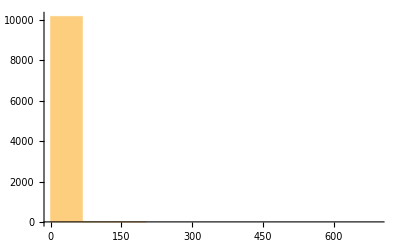

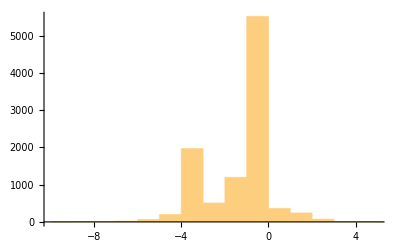

```mathematica
Histogram[dt]
Histogram[Log@dt]
```

```mathematica
First[dt]
```

0.730873

```mathematica
ListPlot3D[{#1[[2]],#1[[1]],#2}&@@@Transpose[{pnts,dt}]]
```

-Graphics3D-

```mathematica
ListPlot3D[{#1[[2]],#1[[1]],#2}&@@@Transpose[{pnts,dt}],PlotRange->{0,10}]
```

-Graphics3D-

```mathematica
ListPlot3D[{#1[[2]],#1[[1]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"points.csv"}]],Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_100_128_points.csv"}]]}]]
```

-Graphics3D-

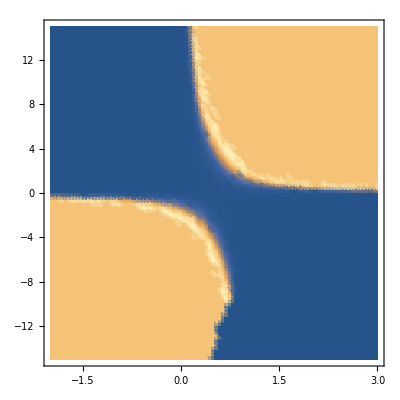

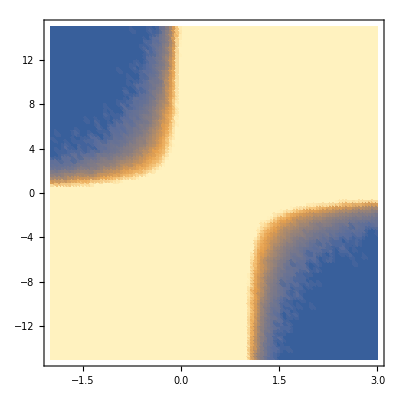

```mathematica
ListDensityPlot[{#1[[2]],#1[[1]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"points.csv"}]],Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_50_128_points.csv"}]]}]]
ListDensityPlot[{#1[[2]],#1[[1]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"points.csv"}]],Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_50_128_points.csv"}]]}],ColorFunctionScaling->False]
```

```mathematica
lines
```

lines

```mathematica
lines=ContourPlot[{(2-1/(1+ⅇ^(β μ))-ⅇ^β/(ⅇ^β+ⅇ^(β μ)))/2==0.250368,(1-1/(1+ⅇ^(β μ)))^4(1-1/(1+ⅇ^(β (μ-1))))^4==0.407,1/128 (18+16 Cosh[β]+Cosh[2 β]) Sech[(β μ)/2]^4 Sech[1/2 (β-β μ)]^4==0.59274,(1/(1+ⅇ^(β μ)))^4(1/(1+ⅇ^(β (μ-1))))^4==0.59274},{μ,-2,3},{β,-15,15},AspectRatio->1,ContourStyle->Directive[Thickness[0.007],kellycols[[6]]](*ContourStyle->{Red,RGBColor[0.09,0.87,1],RGBColor[0.7,1,0],RGBColor[1,0.35,0]*),LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"},PlotPoints->100];
```

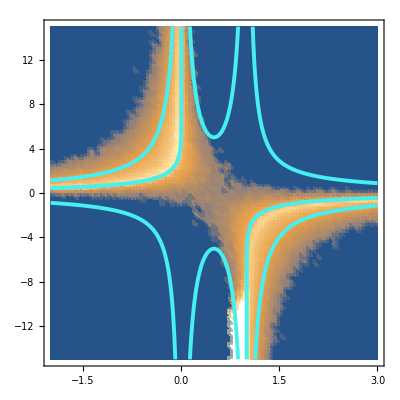

```mathematica
Show[ListDensityPlot[{#1[[2]],#1[[1]],Log[#2]}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"points.csv"}]],Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_50_126_points.csv"}]]}]],lines]
```

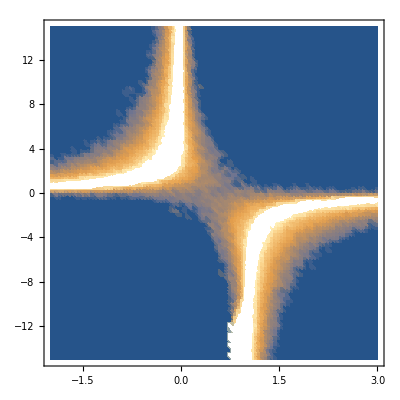

```mathematica
ListDensityPlot[{#1[[2]],#1[[1]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"points.csv"}]],Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_100_128_points.csv"}]]}]]
```

```mathematica
ListPlot3D[{#1[[2]],#1[[1]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"points.csv"}]],Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_100_128_points.csv"}]]}],PlotRange->{0,2}]
```

-Graphics3D-

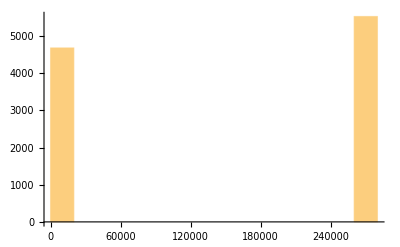

```mathematica
Histogram[Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_50_126_points.csv"}]]]
```

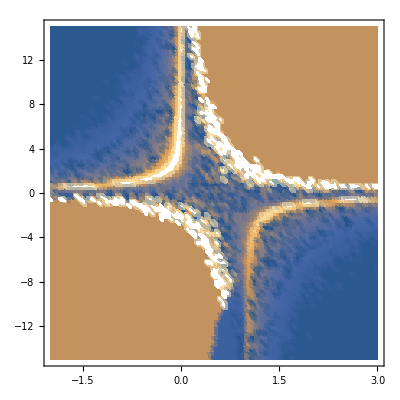

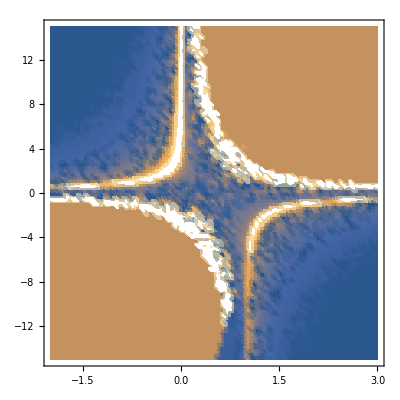

```mathematica
ListDensityPlot[{#1[[2]],#1[[1]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"points.csv"}]],Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_50_512_points.csv"}]]}]]
ListDensityPlot[{#1[[2]],#1[[1]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"points.csv"}]],Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_100_1024_points.csv"}]]}]]
```

```mathematica
ListPointPlot3D[{#1[[2]],#1[[1]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"points.csv"}]],Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_100_1024_points.csv"}]]}],PlotRange->{0,10},ColorFunction->(ColorData["Rainbow"][#3/5]&),ColorFunctionScaling->False,Filling->Bottom]
```

-Graphics3D-

```mathematica
RegionPlot[{(1/(1+ⅇ^(β μ)))^4(1/(1+ⅇ^(β (μ-1))))^4>0.59274,Not[(1/(1+ⅇ^(β μ)))^4(1/(1+ⅇ^(β (μ-1))))^4>0.59274||(1/(1+ⅇ^(β μ)))^4(1/(1+ⅇ^(β (μ-1))))^4>0.59274],(2-1/(1+ⅇ^(β μ))-ⅇ^β/(ⅇ^β+ⅇ^(β μ)))/2>0.250368,1/128 (18+16 Cosh[β]+Cosh[2 β]) Sech[(β μ)/2]^4 Sech[1/2 (β-β μ)]^4>0.59274,(1-1/(1+ⅇ^(β μ)))^4(1-1/(1+ⅇ^(β (μ-1))))^4>0.407},{μ,-3,3},{β,-20,20},BoundaryStyle->Black,PlotLegends->{"Completely Disconnected phase","Minimally Disconnected phase","Amorphous graph phase","Lattice graph phase","Degenerate lattice graph phase"},LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"},PlotStyle->{RGBColor[0.2,0,0.2],RGBColor[0.28,0.11,0.15],RGBColor[0.17,0.46,0.1],RGBColor[0,0,0.39],RGBColor[0.15,0.16,0.15]}]
```

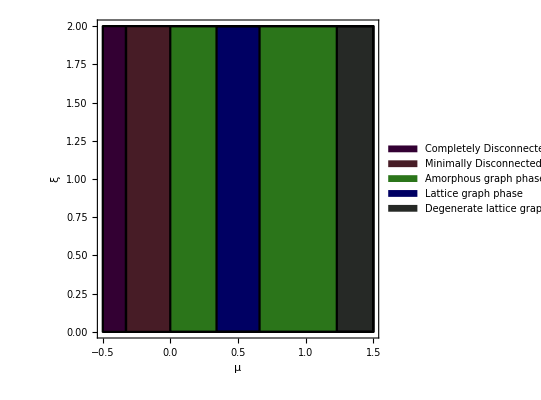

```mathematica
stripes=RegionPlot[{(1/(1+ⅇ^(6 μ)))^4(1/(1+ⅇ^(6 (μ-1))))^4>0.59274,Not[(1/(1+ⅇ^(6 μ)))^4(1/(1+ⅇ^(6 (μ-1))))^4>0.59274||(1/(1+ⅇ^(6 μ)))^4(1/(1+ⅇ^(6 (μ-1))))^4>0.59274],(2-1/(1+ⅇ^(6 μ))-ⅇ^6/(ⅇ^6+ⅇ^(6 μ)))/2>0.250368,1/128 (18+16 Cosh[6]+Cosh[2 6]) Sech[(6 μ)/2]^4 Sech[1/2 (6-6 μ)]^4>0.59274,(1-1/(1+ⅇ^(6 μ)))^4(1-1/(1+ⅇ^(6 (μ-1))))^4>0.407},{μ,-0.5,1.5},{y,0,2},BoundaryStyle->Black,PlotLegends->{"Completely Disconnected phase","Minimally Disconnected phase","Amorphous graph phase","Lattice graph phase","Degenerate lattice graph phase"},LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","ξ"},PlotStyle->{RGBColor[0.2,0,0.2],RGBColor[0.28,0.11,0.15],RGBColor[0.17,0.46,0.1],RGBColor[0,0,0.39],RGBColor[0.15,0.16,0.15]}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"line_points.csv"}],Table[{6,μ},{μ,-0.5,.5,1./200}]]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass 5\line_points.csv

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"line_points2.csv"}],Table[{β,-2},{β,-2.,2.,4./500}]]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass 5\line_points2.csv

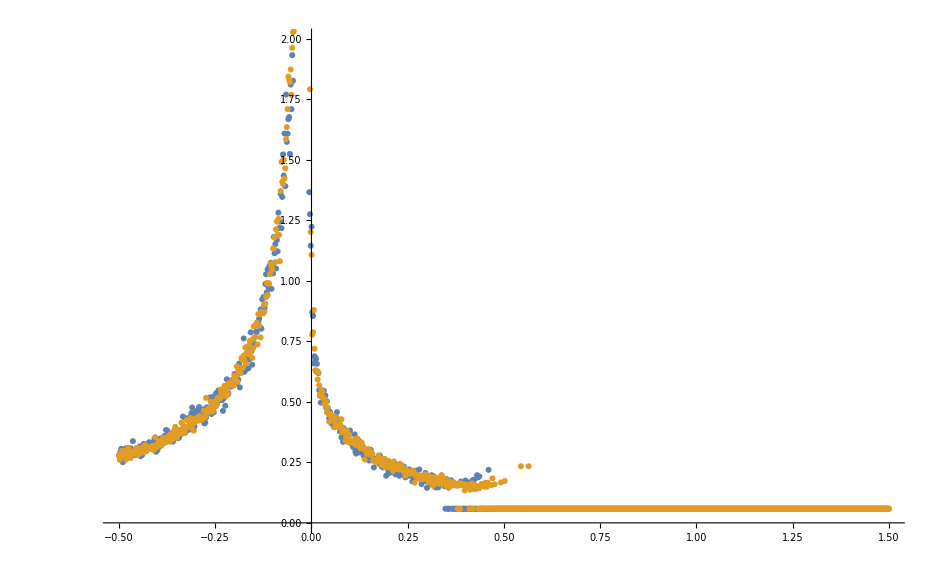

```mathematica
ListPlot[{{#1[[2]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"line_points.csv"}]],Abs@Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_100_128_line_points.csv"}]]}],{#1[[2]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"line_points.csv"}]],Abs@Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_200_256_line_points.csv"}]]}]},PlotRange->{0,2}]
```

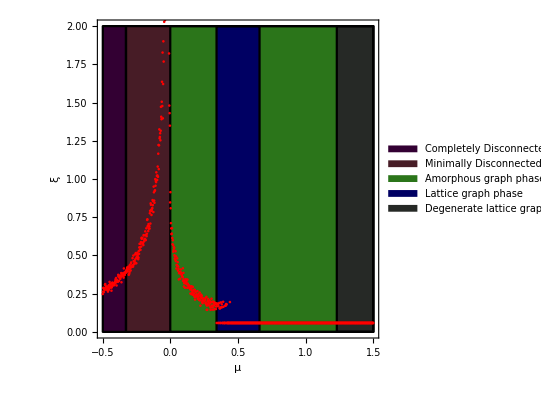

```mathematica
Show[stripes,ListPlot[{#1[[2]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"line_points.csv"}]],Abs@Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_100_128_line_points.csv"}]]}],PlotRange->{0,2},PlotStyle->Red]]
```

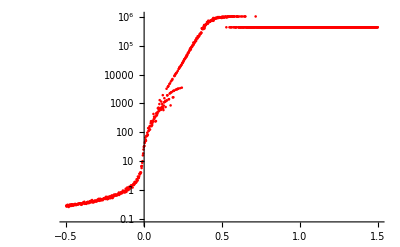

```mathematica
ListLogPlot[{#1[[2]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"line_points.csv"}]],Abs@Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_100_125_line_points.csv"}]]}],PlotRange->All,PlotStyle->Red]
```

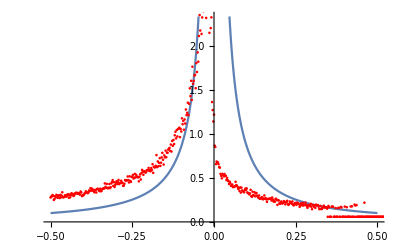

```mathematica
Show[Plot[0.04/Abs[x]^(4/3),{x,-0.5,0.5}],ListPlot[{#1[[2]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"line_points.csv"}]],Abs@Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_100_128_line_points.csv"}]]}],PlotRange->{0,2},PlotStyle->Red]]
```

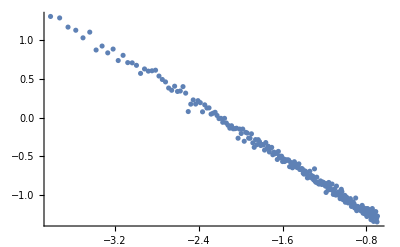

```mathematica
ListPlot[{Log[Abs[#1]],Log[#2]}&@@@Select[{#1[[2]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"line_points.csv"}]],Abs@Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_200_256_line_points.csv"}]]}],#[[1]]<-0.02&]]
```

```mathematica
LinearModelFit[{Log[Abs[#1]],Log[#2]}&@@@Select[{#1[[2]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"line_points.csv"}]],Abs@Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_200_256_line_points.csv"}]]}],#[[1]]<-0.02&],x,x]
```

FittedModel[-1.88863-0.852054 x]

```mathematica
Exp[-1.88]
```

0.15259

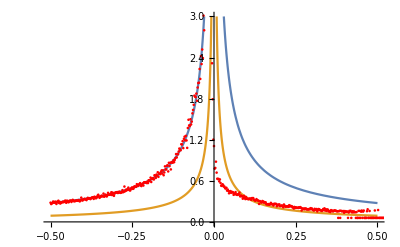

```mathematica
Show[Plot[{0.1525/Abs[x]^0.85,0.05/Abs[x]^0.85},{x,-0.5,0.5},PlotRange->{0,3}],ListPlot[{#1[[2]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"line_points.csv"}]],Abs@Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_200_256_line_points.csv"}]]}],PlotRange->{0,3},PlotStyle->Red]]
```

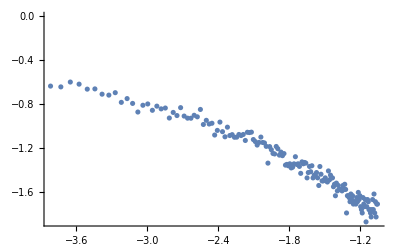

```mathematica
ListPlot[{Log[Abs[#1]],Log[#2]}&@@@Select[{#1[[2]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"line_points.csv"}]],Abs@Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_200_256_line_points.csv"}]]}],0.02<#[[1]]<0.35&]]
```

```mathematica
LinearModelFit[{Log[Abs[#1]],Log[#2]}&@@@Select[{#1[[2]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"line_points.csv"}]],Abs@Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_200_256_line_points.csv"}]]}],0.02<#[[1]]<0.35&],x,x]
```

FittedModel[-2.21175-0.475358 x]

```mathematica
Exp[-2.2]
```

0.110803

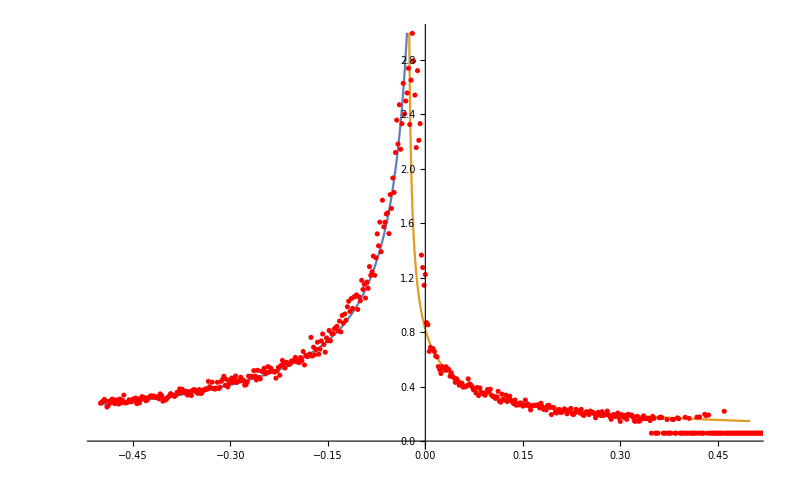

```mathematica
Show[Plot[{0.15/(-x)^0.84,0.10105914848895524/(0.02774965880685605+x)^0.5839667829232333},{x,-0.5,0.5},PlotRange->{0,3}],ListPlot[{#1[[2]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"line_points.csv"}]],Abs@Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_100_128_line_points.csv"}]]}],PlotRange->{0,3},PlotStyle->Red]]
```

```mathematica
NonlinearModelFit[Select[{#1[[2]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"line_points.csv"}]],Abs@Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_200_256_line_points.csv"}]]}],0.0<#[[1]]<0.2&],a/Abs[x-b]^c,{{a,0.1},{b,-0.1},{c,1.}},x,MaxIterations->1000]
```

FittedModel[0.127254/Abs[0.0147009+x]^0.454525]

```mathematica
NonlinearModelFit[Select[{#1[[2]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"line_points.csv"}]],Abs@Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_200_256_line_points.csv"}]]}],#[[1]]<-0.05&],a/(b-x)^c,{{a,0.1},{b,0.},{c,0.8}},x]
```

FittedModel[0.149844/(-0.00203229-x)^0.853846]

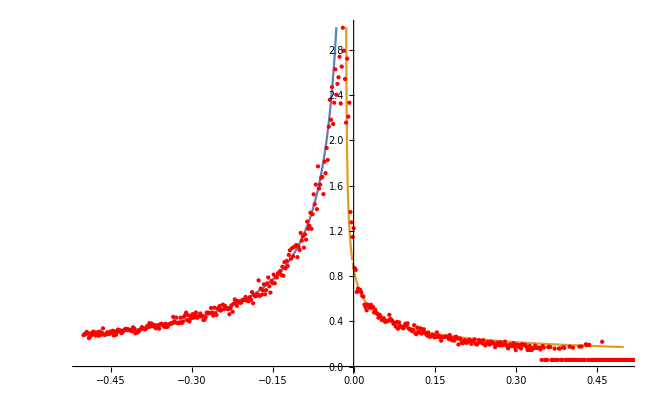

```mathematica
Show[Plot[{0.1498443097471213/(-0.0020322949613413082-x)^0.8538455020763462,0.1272536665262069/(0.01470091869565589+x)^0.45452484937040744},{x,-0.5,0.5},PlotRange->{0,3}],ListPlot[{#1[[2]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"line_points.csv"}]],Abs@Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_100_128_line_points.csv"}]]}],PlotRange->{0,3},PlotStyle->Red]]
```

```mathematica
FittedModel[0.10105914848895524/(0.02774965880685605+x)^0.5839667829232333]["ParameterConfidenceIntervals"]
FittedModel[0.1498443097471213/(-0.0020322949613413082-x)^0.8538455020763462]["ParameterConfidenceIntervals"]
```

{{0.0953276,0.106791},{-0.0335402,-0.0219591},{0.542446,0.625487}}

{{0.144152,0.155537},{-0.00688807,0.00282348},{0.818348,0.889343}}

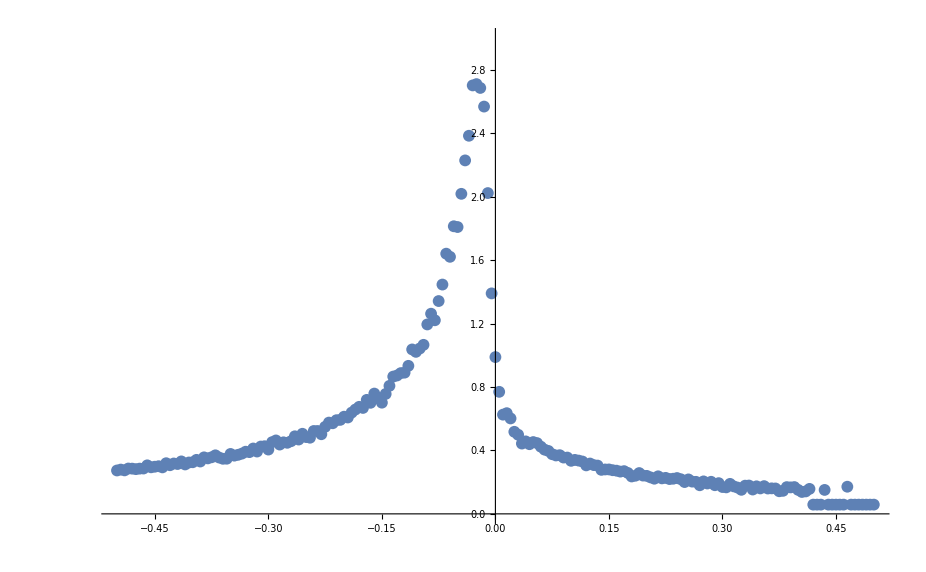

```mathematica
ListPlot[{#1[[2]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"line_points.csv"}]],Abs@Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_100_512_line_points.csv"}]]}],PlotRange->{0,3}]
```